# Mathematica

## Knowledge-based Programming Guo Yunqi

## Brief Introduction

Conceived by Stephen Wolfram

Developed by Wolfram Research

Wolfram Language is the programming language used in Mathematica

## Wolfram Language

Grammar

## Grammar

Expressions

Elements

## Grammar

### Everything is an Expressions

At the core of the Wolfram Language is the foundational idea that everything—data, programs, formulas, graphics, documents—can be represented as symbolic expressions.

e is a λ Expression

e::=x    (a variable)
      |λx.e(a nameless function)
      |e.e(function application)

```mathematica
x
f[]:=1
Sin[x]
```

x+y+z
x y z
x^2
{a,b,c}
a=b

```mathematica
FullForm[x+y+z]
```

Plus[x,y,z]

```mathematica
FullForm[x y z]
```

Times[x,y,z]

```mathematica
FullForm[x^2]
```

Power[x,2]

```mathematica
FullForm[{1,2}]
```

List[1,2]

### Question

What is the full form of  x-y and  x/y in Wolfram Language

```mathematica
FullForm[x/y]
```

## Atomic Elements of Expressions

Symbol

a, hello, Sin, π, ⅇ, ⅈ,

```mathematica
f[a_,b_]:=a+b
```

```mathematica
f[x]
```

1+x

```mathematica
a=1
```

1

```mathematica
f[a_, b_] := a + b
```

1+b

Strings

“abce”

```mathematica
"hello π bold italic α red  "
```

Numbers

Integer

1, 2, -2

```mathematica
divisibleby3[x_Integer]:=(Mod[x,3]==0)
```

```mathematica
divisibleby3[4.5]
```

divisibleby3[4.5]

```mathematica
2^^101
```

5

Real

1.2

```mathematica
2==2.
```

True

```mathematica
2.===2
```

False

```mathematica
2^^1.1101
```

1.8125

Rational

2/3

```mathematica
FullForm[2/3]
```

Rational[2,3]

Complex

1+ⅈ

```mathematica
Exp[1+I]
```

ⅇ^(1+ⅈ)

## List Manipulation

Lists are central constructs in the Wolfram Language, used to represent collections, arrays, sets, and sequences of all kinds. Lists can have any structure and size and can routinely involve even millions of elements.

### What is a list?

```mathematica
l={1,2,3,4}
```

{1,2,3,4}

```mathematica
l2=List[1,2,3,4]
```

{1,2,3,4}

### How to construct a list?

```mathematica
Table[e+1,{e,1,10}]
```

{2,3,4,5,6,7,8,9,10,11}

```mathematica
ParallelTable
```

### Part and Span

```mathematica
l3={1,2,{3,1}}
```

{1,2,{3,1}}

```mathematica
l3[[3]][[2]]
```

4

Some other functions to manipulate lists

```mathematica
Length[l3]
```

3

```mathematica
Position[l3,1]
```

{{1},{3,2}}

```mathematica
MemberQ[l3,4]
```

False

```mathematica
Append[l3,3]
```

{1,2,{3,1},4,3}

```mathematica
AppendTo[l3,3]
```

## Advanced Mathematics

Find the turning points on a plane curve

x^3+3 x^2-3x-1

```mathematica
g[x_]:=x^3+3 x^2-3x-1
```

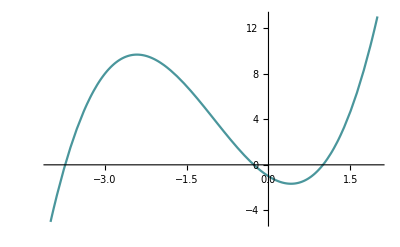

```mathematica
Plot[g[x],{x,-4,2}]
```

```mathematica
Solve[g'[x]==0,x]
```

{{x→-1-√2},{x→-1+√2}}

## Probability and Statistics

Two trains arrive at a station independently and stay for 10 minutes. If the arrival times are uniformly distributed, find the probability the two trains will meet at the station within one hour.

```mathematica
Probability[Abs[x-y]<10,{x,y}\[Distributed]UniformDistribution[{{0,60},{0,60}}]]
```

11/36

## Linear Algebra

Exact inverse of a Hilbert matrix:

HilbertMatrix[5] = (1 | 1/2 | 1/3 | 1/4 | 1/5
1/2 | 1/3 | 1/4 | 1/5 | 1/6
1/3 | 1/4 | 1/5 | 1/6 | 1/7
1/4 | 1/5 | 1/6 | 1/7 | 1/8
1/5 | 1/6 | 1/7 | 1/8 | 1/9)

```mathematica
inversematrix=Inverse[({{1, 1/2, 1/3, 1/4, 1/5}, {1/2, 1/3, 1/4, 1/5, 1/6}, {1/3, 1/4, 1/5, 1/6, 1/7}, {1/4, 1/5, 1/6, 1/7, 1/8}, {1/5, 1/6, 1/7, 1/8, 1/9}})]//MatrixForm
```

(25 | -300 | 1050 | -1400 | 630
-300 | 4800 | -18900 | 26880 | -12600
1050 | -18900 | 79380 | -117600 | 56700
-1400 | 26880 | -117600 | 179200 | -88200
630 | -12600 | 56700 | -88200 | 44100)

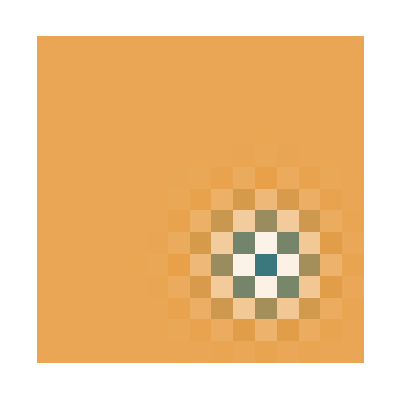

```mathematica
ArrayPlot[Inverse[HilbertMatrix[15]]]
```

## Computer Engineering

Detect Faces in Real Time

```mathematica
Dynamic[image=CurrentImage[];
faces=FindFaces[image];
Show[{image,Graphics[{EdgeForm[{Red,Thick}],FaceForm[],Rectangle@@@faces}]}]]
```

## Nature Language Processing

NLG: Describe the result of a mathematical expression

∫1/(1+x^3)ⅆx

```mathematica
SpokenString[∫1/(1+x^3) ⅆx]
```

arc tangent of the quantity the quantity 2 times x minus 1 over square root of 3 over square root of 3 plus 1 third times logarithm of the quantity 1 plus x minus 1 sixth times logarithm of the quantity 1 minus x plus x squared

Processing textual data: Make a two-step synonym network for the word “gril”:

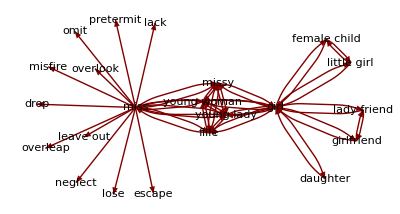

```mathematica
GraphPlot[Flatten[Rest[NestList[Union[Flatten[Thread[# -> WordData[#, "Synonyms", "List"]] & /@ Last /@ #]] &, {"" -> "girl"}, 2]]], VertexLabeling -> True, DirectedEdges -> True, ImageSize -> Full]
```

## Network Processing

Here is a network of a group of people, find their community

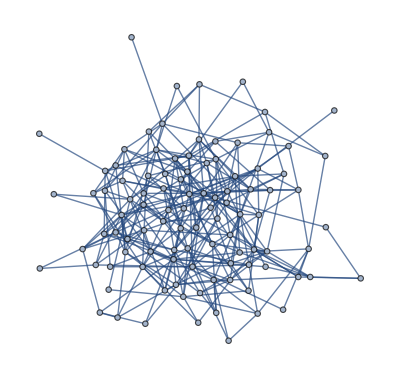

```mathematica
RandomGraph[{100,290}]
```

```mathematica
CommunityGraphPlot[-Graphics-]
```

-Graphics-

## Machine Learning

Train a digit recognizer on 100 examples from the MNIST database of handwritten digits

Database:

```mathematica
data={-Graphics-->2,-Graphics-->5,-Graphics-->8,-Graphics-->0,-Graphics-->2,-Graphics-->7,-Graphics-->5,-Graphics-->1,-Graphics-->3,-Graphics-->0,-Graphics-->3,-Graphics-->9,-Graphics-->6,-Graphics-->2,-Graphics-->8,-Graphics-->2,-Graphics-->0,-Graphics-->6,-Graphics-->6,-Graphics-->1,-Graphics-->1,-Graphics-->7,-Graphics-->8,-Graphics-->5,-Graphics-->0,-Graphics-->4,-Graphics-->7,-Graphics-->6,-Graphics-->0,-Graphics-->2,-Graphics-->5,-Graphics-->3,-Graphics-->1,-Graphics-->5,-Graphics-->6,-Graphics-->7,-Graphics-->5,-Graphics-->4,-Graphics-->1,-Graphics-->9,-Graphics-->3,-Graphics-->6,-Graphics-->8,-Graphics-->0,-Graphics-->9,-Graphics-->3,-Graphics-->0,-Graphics-->3,-Graphics-->7,-Graphics-->4,-Graphics-->4,-Graphics-->3,-Graphics-->8,-Graphics-->0,-Graphics-->4,-Graphics-->1,-Graphics-->3,-Graphics-->7,-Graphics-->6,-Graphics-->4,-Graphics-->7,-Graphics-->2,-Graphics-->7,-Graphics-->2,-Graphics-->5,-Graphics-->2,-Graphics-->0,-Graphics-->9,-Graphics-->8,-Graphics-->9,-Graphics-->8,-Graphics-->1,-Graphics-->6,-Graphics-->4,-Graphics-->8,-Graphics-->5,-Graphics-->8,-Graphics-->0,-Graphics-->6,-Graphics-->7,-Graphics-->4,-Graphics-->5,-Graphics-->8,-Graphics-->4,-Graphics-->3,-Graphics-->1,-Graphics-->5,-Graphics-->1,-Graphics-->9,-Graphics-->9,-Graphics-->9,-Graphics-->2,-Graphics-->4,-Graphics-->7,-Graphics-->3,-Graphics-->1,-Graphics-->9,-Graphics-->2,-Graphics-->9,-Graphics-->6};
```

```mathematica
c=Classify[data]
```

ClassifierFunction[…]

Use the classifier to recognize unseen digits:

```mathematica
c[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

{0,1,2,3,4,1,4,7,8,9}

```mathematica
c[-Graphics-,"TopProbabilities"]
```

{4→0.451554,6→0.255324,0→0.242137}

#### Homework

Use classify function to seperate paper data to different topics

## Review

Brief introduction

Wolfram Language

Grammar

Expression

Elements

List

Examples

Maths

Computer Science

Homework

## Reference

Wolfram Documentation

wolfram.com

blog.wolfram.com